# Mtb dynamics in rabbits with Sherman’s pBP10 plasmid: understanding mechanisms controlling bacterial replication

```mathematica
Get[$HomeDirectory<>"/refs/mathematica/my_packages/tools.m"]
Get[$HomeDirectory<>"/refs/mathematica/my_packages/bootstrap-2m.m"]
Get[$HomeDirectory<>"/refs/mathematica/my_packages/tests.m"]
Get[$HomeDirectory<>"/refs/mathematica/my_packages/graphics-12-1.m"]
PicturesPath=$HomeDirectory<>"/research/immunology/tb/rabbits/replication-clock-plasmid";
```

In vitro data

## Plasmid loss in vitro (s=0.10)

### In vitro data (Exp 3): HN878 (s=0.10)

```mathematica
dataVitro=Import[PicturesPath<>"/data/selvakumar_u17/data-HN878_pBP10-invitro-invivo-TOSHARE.xlsx","XLSX"][[1]];
%//TableForm
Import[PicturesPath<>"/data/selvakumar_u17/HN878_PBP_PLASMID_REPL_DATA-edited.csv","CSV"];

Transpose[{Range[Length[dataVitro[[1]]]],dataVitro[[1]]}]//TableForm
```

plate type | media:day | 0. | 3. | 6. | 9. | 12. | 15. | 18. | 21.
7H11 | 7H9 | 6.9×10^7 | 6.6×10^7 | 7.15×10^7 | 7.×10^7 | 7.55×10^7 | 7.75×10^7 | 8.1×10^7 | 7.75×10^7
7H11 | 7H9 | 7.×10^7 | 7.6×10^7 | 7.4×10^7 | 7.3×10^7 | 7.1×10^7 | 7.×10^7 | 7.05×10^7 | 8.45×10^7
7H11 | 1:3 7H9 | 7.×10^7 | 2.×10^7 | 1.×10^7 | 6.65×10^6 | 7.75×10^6 | 7.6×10^6 | 6.6×10^6 | 6.9×10^6
7H11 | 1:3 7H9 | 6.8×10^7 | 2.4×10^7 | 9.×10^6 | 7.95×10^6 | 7.2×10^6 | 7.4×10^6 | 7.4×10^6 | 6.65×10^6
7H11+KAN | 7H9 | 7.×10^7 | 4.3×10^7 | 2.6×10^7 | 1.75×10^7 | 1.5×10^7 | 1.4×10^7 | 1.1×10^7 | 9.5×10^6
7H11+KAN | 7H9 | 6.8×10^7 | 4.6×10^7 | 2.4×10^7 | 1.8×10^7 | 1.4×10^7 | 1.2×10^7 | 1.3×10^7 | 1.2×10^7
7H11+KAN | 1:3 7H9 | 6.6×10^7 | 1.5×10^7 | 4.×10^6 | 2.7×10^6 | 2.2×10^6 | 2.1×10^6 | 2.05×10^6 | 1.8×10^6
7H11+KAN | 1:3 7H9 | 6.9×10^7 | 1.4×10^7 | 3.4×10^6 | 2.5×10^6 | 2.45×10^6 | 2.25×10^6 | 2.×10^6 | 1.95×10^6

1 | plate type
2 | media:day
3 | 0.
4 | 3.
5 | 6.
6 | 9.
7 | 12.
8 | 15.
9 | 18.
10 | 21.

```mathematica
step=4;
alldata=Table[Transpose[{dataVitro[[1]],dataVitro[[i+1]],dataVitro[[i+1+step]]}],{i,1,step}]
```

{{{plate type,7H11,7H11+KAN},{media:day,7H9,7H9},{0.,6.9×10^7,7.×10^7},{3.,6.6×10^7,4.3×10^7},{6.,7.15×10^7,2.6×10^7},{9.,7.×10^7,1.75×10^7},{12.,7.55×10^7,1.5×10^7},{15.,7.75×10^7,1.4×10^7},{18.,8.1×10^7,1.1×10^7},{21.,7.75×10^7,9.5×10^6}},{{plate type,7H11,7H11+KAN},{media:day,7H9,7H9},{0.,7.×10^7,6.8×10^7},{3.,7.6×10^7,4.6×10^7},{6.,7.4×10^7,2.4×10^7},{9.,7.3×10^7,1.8×10^7},{12.,7.1×10^7,1.4×10^7},{15.,7.×10^7,1.2×10^7},{18.,7.05×10^7,1.3×10^7},{21.,8.45×10^7,1.2×10^7}},{{plate type,7H11,7H11+KAN},{media:day,1:3 7H9,1:3 7H9},{0.,7.×10^7,6.6×10^7},{3.,2.×10^7,1.5×10^7},{6.,1.×10^7,4.×10^6},{9.,6.65×10^6,2.7×10^6},{12.,7.75×10^6,2.2×10^6},{15.,7.6×10^6,2.1×10^6},{18.,6.6×10^6,2.05×10^6},{21.,6.9×10^6,1.8×10^6}},{{plate type,7H11,7H11+KAN},{media:day,1:3 7H9,1:3 7H9},{0.,6.8×10^7,6.9×10^7},{3.,2.4×10^7,1.4×10^7},{6.,9.×10^6,3.4×10^6},{9.,7.95×10^6,2.5×10^6},{12.,7.2×10^6,2.45×10^6},{15.,7.4×10^6,2.25×10^6},{18.,7.4×10^6,2.×10^6},{21.,6.65×10^6,1.95×10^6}}}

```mathematica
media=Split[Sort[Drop[dataVitro[[All,2]],1]]][[All,1]];
media={"7H9","1:3 7H9"}
alldata0=Table[Flatten[Cases[alldata,x_?(#[[2,2]]==media[[med]]&):>Drop[x,2]],1],{med,1,Length[media]}];
alldata0=Map[Map[Append[#,100*#[[3]]/#[[2]]]&,#]&,alldata0];
```

{7H9,1:3 7H9}

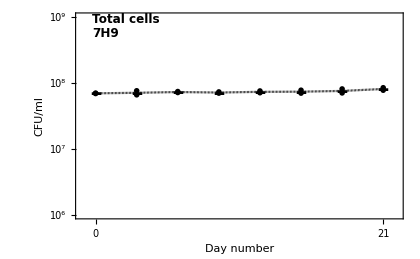
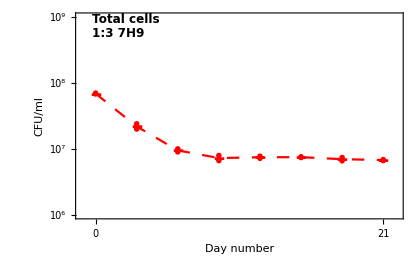

```mathematica
xt=Table[{i,i,{0.02,0}},{i,0,17*7,3}];
myFig1=Table[
temp1=ToLogOne[alldata0[[i]][[All,{1,2}]]];
Show[
MyListPlot[temp1,
PlotRange->{{-1,22},{6,9}},
Epilog->{
mylegend2noS[{"Total cells",media[[i]]},{0.0,0.97},FontColor->{Black,Black}]
},
PlotStyle->{{colors[[i]],dashings[[i]]}},
PlotMarkers->{symbols[[i]],12},
FrameLabel->{"Day number", "CFU/ml"},
FrameTicks->{xt,logticks[{5,10,1}]}
],
MyListPlot[{AverageDataOne[temp1]},
Joined->True,
PlotStyle->{{colors[[i]],dashings[[i]]}},
PlotMarkers->Line
]
],
{i,1,Length[alldata0]}
]
```

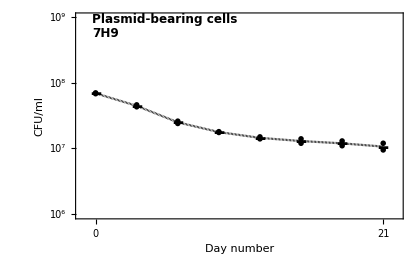
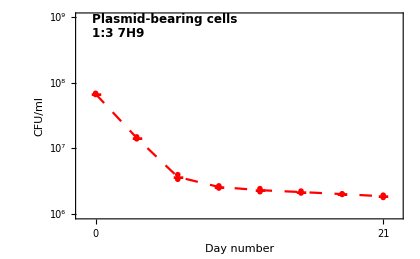

```mathematica
xt=Table[{i,i,{0.02,0}},{i,0,17*7,3}];
myFig2=Table[
temp1=ToLogOne[alldata0[[i]][[All,{1,3}]]];
Show[
MyListPlot[temp1,
PlotRange->{{-1,22},{5.99,9}},
Epilog->{
mylegend2noS[{"Plasmid-bearing cells",media[[i]]},{0.0,0.97},FontColor->{Black,Black}]
},
PlotStyle->{{colors[[i]],dashings[[i]]}},
PlotMarkers->{symbols[[i]],12},
FrameLabel->{"Day number", "CFU/ml"},
FrameTicks->{xt,logticks[{5,10,1}]}
],
MyListPlot[{AverageDataOne[temp1]},
Joined->True,
PlotStyle->{{colors[[i]],dashings[[i]]}},
PlotMarkers->Line
]
],
{i,1,Length[alldata0]}
]
```

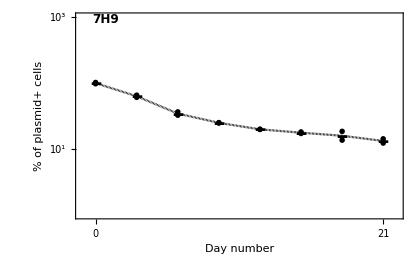
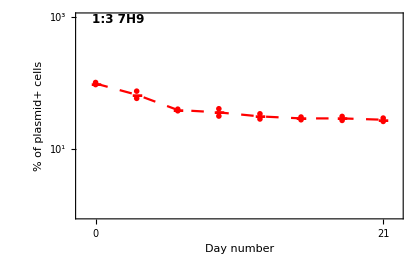

```mathematica
xt=Table[{i,i,{0.02,0}},{i,0,17*7,3}];
myFig3=Table[
temp1=ToLogOne[alldata0[[i]][[All,{1,4}]]];
Show[
MyListPlot[temp1,
PlotRange->{{-1,22},{0,3}},
Epilog->{
mylegend2noS[{media[[i]]},{0.0,0.97},FontColor->{Black,Black}]
},
PlotStyle->{{colors[[i]],dashings[[i]]}},
PlotMarkers->{symbols[[i]],12},
FrameLabel->{"Day number", "% of plasmid+ cells"},
FrameTicks->{xt,logticks[{-3,3,1}]}
],
MyListPlot[{AverageDataOne[temp1]},
Joined->True,
PlotStyle->{{colors[[i]],dashings[[i]]}},
PlotMarkers->Line
]
],
{i,1,Length[alldata0]}
]
```

```mathematica
{myFig1,myFig2,myFig3}
MyGraphicsArray[%];
```

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

```mathematica
Export[PicturesPath<>"/figs/data-HN878-pBP10-exp3-vitro-transfers.pdf",%,"PDF"];
```

```mathematica
(* Vary the data to be included in the regressions & dt *)

dilution=1/10;
dt=3;
alldata0N=Map[Map[{#[[1]],If[#[[1]]≤1,1,(1/dilution)^(#[[1]]/dt)]*#[[2]],If[#[[1]]≤1,1,(1/dilution)^(#[[1]]/dt)]*#[[3]],#[[4]]}&,#]&,alldata0];

t1=0;
t2=120;

temp1=Table[Cases[ToLogOne[alldata0N[[i]][[All,{1,2}]]],x_?(#[[1]]≥t1&&#[[1]]≤t2&)],{i,1,Length[alldata0N]}];

r=Map[Log[10]*Fit[#,{1,x},x][[2,1]]&,temp1]
Print["Doubling time = ",Td=24*Log[2]/r," h"]

temp2=Table[Cases[ToLogOne[alldata0N[[i]][[All,{1,3}]]],x_?(#[[1]]≥t1&&#[[1]]≤t2&)],{i,1,Length[alldata0N]}];
rp=Map[Log[10]*Fit[#,{1,x},x][[2,1]]&,temp2]

temp3=Table[Cases[ToLogOne[alldata0N[[i]][[All,{1,4}]]],x_?(#[[1]]≥t1&&#[[1]]≤t2&)],{i,1,Length[alldata0N]}];
rs=-Map[Log[10]*Fit[#,{1,x},x][[2,1]]&,temp3]

Print["Time ",t1,"-",t2," days; s= ",rs/r," and mean = ",Mean[rs/r]];

temp4=Table[Map[{#[[1]]*r[[i]]/Log[2],Log10[#[[2]]]}&,alldata0N[[i]][[All,{1,4}]]],{i,1,Length[alldata0N]}];

Print["Estimate by pulling data together (generations) = ",s2=-Fit[Flatten[N[Map[Cases[#,x_?(#[[1]]<=t2&&#[[1]]≥t1&)]&,temp4]],1],{1,x},x][[2,1]]*Log[2,10]];
```

{0.773287,0.677695}

Doubling time = {21.5128,24.5472} h

{0.681021,0.622183}

{0.0922657,0.0555128}

Time 0-120 days; s= {0.119316,0.081914} and mean = 0.100615

Estimate by pulling data together (generations) = 0.105546

```mathematica
(* generations *)
fit1=LinearModelFit[Flatten[N[Map[Cases[#,x_?(#[[1]]<=t2&&#[[1]]≥t1&)]&,temp4]],1],{1,x},x];
-fit1["ParameterConfidenceIntervals"][[2]]*Log[2,10]
```

{0.125008,0.0860838}

```mathematica
temp1=Table[ToLogOne[alldata0N[[i]][[All,{1,2}]]],{i,1,Length[alldata0N]}];

Print["Doubling time = ",Td=24*Log[2]/r," h"]
lab=Table[media[[i]]<>": r="<>ToString[MyRound[r[[i]],2]]<>"/h",{i,1,Length[media]}];

xt=Table[{i,i,{0.02,0}},{i,0,17*7,3}];

myFig3a=Show[
MyListPlot[temp1,
PlotRange->{{-0.5,22},{5,15}},
Epilog->{
mylegend2noS[{"Total cells (including dilution)"},{0.0,0.97},FontColor->{Black,Black}],
mylegend3[lab,{0.05,0.88}],
{Dashed,Line[{Scaled[{(t2)/24,0}],Scaled[{(t2)/24,0.7}]}]}
},
FrameLabel->{"Days in culture", "CFU/ml"},
FrameTicks->{xt,logticks3[{5,25,5}]}
],
MyListPlot[AverageData[temp1],
Joined->True,
PlotMarkers->Line
]
];

temp2=Table[ToLogOne[alldata0N[[i]][[All,{1,3}]]],{i,1,Length[alldata0N]}];
(* rp=Map[Log[10]*Fit[#,{1,x},x][[2,1]]&,temp2] *)
lab=Table[media[[i]]<>": r*(1-s)="<>ToString[MyRound[rp[[i]],2]]<>"/h",{i,1,Length[media]}];

myFig3b=Show[
MyListPlot[temp2,
PlotRange->{{-0.5,22},{5,15}},
Epilog->{
mylegend2noS[{"Plasmid-bearing cells (including dilution)"},{0.0,0.97},FontColor->{Black,Black}],
mylegend3[lab,{0.05,0.88}],
{Dashed,Line[{Scaled[{(t2)/24,0}],Scaled[{(t2)/24,0.7}]}]}
},
FrameLabel->{"Days in culture", "CFU/ml"},
FrameTicks->{xt,logticks3[{5,15,5}]}
],
MyListPlot[AverageData[temp2],
Joined->True,
PlotMarkers->Line
]
];

temp3=Table[ToLogOne[alldata0N[[i]][[All,{1,4}]]],{i,1,Length[alldata0N]}];
(* rs=-Map[Log[10]*Fit[#,{1,x},x][[2,1]]&,temp3] *)
lab=Table[media[[i]]<>": r*s="<>ToString[MyRound[rs[[i]],2]]<>"/h (s="<>ToString[MyRound[(rs/r)[[i]],2]]<>")",{i,1,Length[media]}];

myFig3c=Show[
MyListPlot[temp3,
PlotRange->{{-0.5,22},{0,3}},
Epilog->{
mylegend2noS[{"HN878-pBP10"},{0.0,0.97},FontColor->{Black,Black}],
mylegend3[lab,{0.05,0.88}],
{Dashed,Line[{Scaled[{(t2)/24,0}],Scaled[{(t2)/24,0.7}]}]}
},
FrameLabel->{"Days in culture", "% plasmid-bearing cells"},
FrameTicks->{xt,logticks3[{-2,3,1}]}
],
MyListPlot[AverageData[temp3],
Joined->True,
PlotMarkers->Line
]
];

temp4=Table[Map[{#[[1]]*r[[i]]/Log[2],Log10[#[[2]]]}&,alldata0N[[i]][[All,{1,4}]]],{i,1,Length[alldata0N]}];
Print["Plasmid loss coefficient per generation = ",s0=-Map[Fit[#,{1,x},x][[2,1]]&,temp4]*Log[2,10]];
lab=Table[media[[i]]<>": s="<>ToString[MyRound[s0[[i]],2]]<>" (all data)",{i,1,Length[media]}];

myFig3d=Show[
MyListPlot[temp4,
PlotRange->{{-0.5,25},{0,3}},
Epilog->{
mylegend2noS[{"HN878-pBP10"},{0.0,0.97},FontColor->{Black,Black}],
mylegend3[lab,{0.05,0.88}]
},
FrameLabel->{"Generations", "% plasmid-bearing cells"},
FrameTicks->{myticks,logticks3[{-2,3,1}]}
],
MyListPlot[AverageData[temp4],
Joined->True,
PlotMarkers->Line
]
];
Print["Plasmid loss coefficient = ",s=rs/r];
Print["Mean s = ",Mean[s]];

{{myFig3a,myFig3b},{myFig3c,myFig3d}}
MyGraphicsArray[%];
```

Doubling time = {21.5128,24.5472} h

Plasmid loss coefficient per generation = {0.119316,0.081914}

Plasmid loss coefficient = {0.119316,0.081914}

Mean s = 0.100615

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

```mathematica
Export[PicturesPath<>"/figs/data-HN878-pBP10-exp3-vitro-vs-time-generation-t1-"<>ToString[t1]<>"-t2-"<>ToString[t2]<>"-4panels.pdf",%,"PDF"];
```

Fitting models to in vivo data

## 1 granuloma in the lung: corrected data (March 2021, s=0.10)

### Full model (s=0.10): fitting 16wk data - total and % weighted least squares: best fit

```mathematica
data=Import[PicturesPath<>"/data/selvakumar_u17/data-HN878_pBP10-invitro-invivo-TOSHARE.xlsx","XLSX"][[2]];
%//TableForm;

Transpose[{Range[Length[data[[1]]]],data[[1]]}]//TableForm
```

1 | time (weeks)
2 | animal ID
3 | Mtb strain
4 | Mtb type
5 | left or right lung
6 | weight of tissue, g
7 | CFU/tissue
8 | tissue

```mathematica
times=Split[Sort[Drop[data[[All,1]],1]]][[All,1]]
animals=Split[Sort[Drop[data[[All,2]],1]]][[All,1]]
Length[animals]
lung={"left","right"};
Mtb={"HN878","HN878+pBP10"};
Split[Sort[Drop[data[[All,4]],1]]][[All,1]];
type={"sensitive","sensitive+resistant","resistant"};
```

{0.,4.,8.,12.,16.,}

{506.,507.,509.,510.,511.,512.,513.,514.,515.,516.,517.,518.,519.,520.,521.,522.,523.,524.,525.,526.,527.,528.,529.,}

24

```mathematica
(* HN878+pBP10: percent of plasmid-bearing cells *)

subset=Split[Sort[Cases[data,x_?(#[[3]]==Mtb[[2]]&):>x[[2]]]]][[All,1]];
j=1; (* lung *)
i=2; (* animal *)
tt1=Cases[data,x_?(#[[2]]==subset[[i]]&&#[[5]]==lung[[j]]&&#[[4]]=="sensitive+resistant"&)][[1]]
tt2=Cases[data,x_?(#[[2]]==subset[[i]]&&#[[5]]==lung[[j]]&&#[[4]]=="resistant"&)][[1]]
```

{8.,520.,HN878+pBP10,sensitive+resistant,left,14.7,1.3617×10^7,lung}

{8.,520.,HN878+pBP10,resistant,left,14.7,1.7595×10^6,lung}

```mathematica
Clear[i,j];
alldata=Table[
Table[
tt1=Cases[data,x_?(#[[2]]==subset[[i]]&&#[[5]]==lung[[j]]&&#[[4]]=="sensitive+resistant"&)][[1]];
tt2=Cases[data,x_?(#[[2]]==subset[[i]]&&#[[5]]==lung[[j]]&&#[[4]]=="resistant"&)][[1]];
{tt1[[1]]*7,tt1[[7]],tt2[[7]],N[100*tt2[[7]]/tt1[[7]]],lung[[j]]},
{i,1,Length[subset]}],{j,1,Length[lung]}
]
```

{{{28.,2.69151×10^7,844537.,3.13778,left},{56.,1.3617×10^7,1.7595×10^6,12.9213,left},{84.,2.00791×10^6,86053.5,4.28571,left},{56.,1.42194×10^6,175299.,12.3281,left},{0.,314.666,184.663,58.6854,left},{112.,3.2883×10^10,2.46164×10^8,0.748607,left},{28.,2.69242×10^7,989432.,3.67488,left},{56.,739500.,40179.5,5.43333,left},{84.,1.58871×10^6,1556.29,0.0979592,left},{0.,340.8,277.752,81.5,left},{112.,3.48491×10^6,37322.3,1.07097,left}},{{28.,3.51333×10^7,2.76911×10^6,7.88172,right},{56.,2.52923×10^7,2.46267×10^6,9.73684,right},{84.,5.27132×10^6,124471.,2.36129,right},{56.,6.28801×10^6,346874.,5.51643,right},{0.,969.588,714.433,73.6842,right},{112.,1.69568×10^10,2.72023×10^8,1.60421,right},{28.,3.62469×10^7,969553.,2.67486,right},{56.,8.25516×10^6,539371.,6.53374,right},{84.,3.34004×10^6,4128.67,0.123611,right},{0.,847.895,657.966,77.6,right},{112.,2.20479×10^7,108800.,0.493471,right}}}

```mathematica
alldata0=Cases[Flatten[alldata,1],x_?(#[[1]]≤16*7&)];
fitdataL=alldata[[All,1]];
fitdataR=alldata[[All,2]];
```

```mathematica
fitdata1=alldata0[[All,{1,2}]];
fitdata2=alldata0[[All,{1,3}]];
fitdata3=alldata0[[All,{1,4}]];
Print["Total error = ",lof0[ToLogOne[fitdata1]][[1]]+lof0[ToLogOne[fitdata3]][[1]]];
```

Total error = 16.8388

-Graphics-

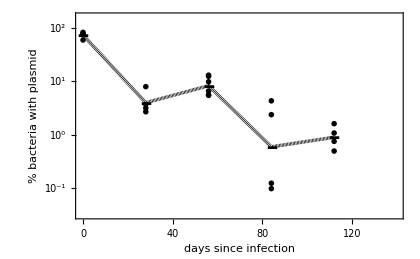

```mathematica
Show[
MyListPlot[
ToLog[{fitdata1,fitdata2}],
Epilog->mylegend3[{"total bacteria","bacteria with plasmid"},{0.05,0.95}],
PlotRange->{{-0.5,140},{1.999,12.0001}},
FrameLabel->{"days since infection","bacterial count"},
FrameTicks->{myticks,logticks3[{2,12,2}]}
],
MyListPlot[AverageData[ToLog[{fitdata1,fitdata2}]],
SymbolShape->Line,
Joined->True
]
]

DisplayTogether[
MyListPlot[
{Map[{#[[1]],Log[10,#[[2]]]}&,fitdata3]},
PlotRange->{{-0.5,140},{-1.5001,2.2001}},
FrameLabel->{"days since infection","% bacteria with plasmid"},
FrameTicks->{myticks,logticks3[{-3,2,1}]}
],
MyListPlot[{AverageDataOne[Map[{#[[1]],Log[10,#[[2]]]}&,fitdata3]]},
SymbolShape->Line,
Joined->True
]
]
```

```mathematica
Clear[ssrV2,parV,array];

ssrV2[array_,parV_/;VectorQ[parV,NumericQ],type___]:=Module[
{r1,r2,r3,d1,d2,d3,sol,pp,ff,p0,f0,r,d,ff0,result,p,f,sigma1,sigma2,sigma,ff1,r4,d4},
{r1,r2,r3,r4,d1,d2,d3,d4,p0,f0,sigma1,sigma2}=parV;
r[t_]:=If[t<t1,r1,If[t<t2,r2,If[t<t3,r3,r4]]];
d[t_]:=If[t<t1,d1,If[t<t2,d2,If[t<t3,d3,d4]]];
sigma={sigma1,sigma2};

sol=NDSolve[
{
p'[t]==r[t]*(1-s)*p[t]-d[t]*p[t],p[0]==p0,
f'[t]==s*r[t]*p[t]+r[t]*f[t]-d[t]*f[t],f[0]==f0},
{p[t],f[t]},
{t,0,tmax},
Method->Automatic
];

pp[t1_]:=First[p[t]/.sol]/.t->t1;
ff[t1_]:=First[f[t]/.sol]/.t->t1;
ff1[t_]:={pp[t]+ff[t],pp[t]};
ff0[t_]:={pp[t]+ff[t],100*pp[t]/(pp[t]+ff[t])};

result=
Which[
type==1,Table[Map[(Log[10,ff0[#[[1]]][[i]]]-Log[10,#[[2]]])&,array[[i]]],{i,1,Length[array]}],
type==2,Total[
Flatten[Table[
Map[(Log[10,ff0[#[[1]]][[i]]]-Log[10,#[[2]]])^2/(2*sigma[[i]]^2)&,array[[i]]]+Length[array[[i]]]*Log[sigma[[i]]],
{i,1,Length[array]}
],1]],
type==3,ff1[t],
type==4,{pp[t]/(pp[t]+ff[t])},
type==6,Total[Flatten[Table[Map[(Log[10,ff0[#[[1]]][[i]]]-Log[10,#[[2]]])^2&,array[[i]]],{i,1,Length[array]}]]]
];
Clear[ff0,pp,ff,sol];
result
];

eps=10;
pow=2;


t1=4*7;
t2=8*7;
t3=12*7;
t4=16*7;
allT={t1,t2,t3,t4};

tmax=allT[[-1]];
```

```mathematica
(* Full model *)

datasetT={fitdata1,fitdata3};

s=0.10; (* sigma1 and sigma2 *)
AllPars={{r1,0.8851970533712552,0},{r2,5.443814236764476*^-11,0},{r3,0.676516353184589,0},{r4,0.16819380083619023,0},{d1,0.4944105020955814,0},{d2,0.06399817596904057,0},{d3,0.6918853013909989,0},{d4,1.9054508834804458*^-8,0},{p0,398.4985812112027,0},{f0,148.62813396493152,0},{sigma1,0.17191160497294267,0},{sigma2,0.0804842401927369,0}};


{ParF,Par0,FixedPars}=Transpose[AllPars];

pars=Table[If[FixedPars[[i]]==0,ParF[[i]]^pow,Par0[[i]]],{i,1,Length[ParF]}];
pars0=Cases[Table[If[FixedPars[[i]]==0,{ParF[[i]],Par0[[i]]^(1/pow),1.01*Par0[[i]]^(1/pow)}],{i,1,Length[ParF]}],x_?(VectorQ[#]&)];
pars0=Split[Sort[pars0]][[All,1]];
ParD=(ParF*(1-FixedPars)+Par0*FixedPars);
Print["Parameters to be fitted ",pars0[[All,1]]];
eps=8;

tStart=SessionTime[];
ssrV2[datasetT,Par0,2]
tEnd=SessionTime[];
Print["Calculated in ",tEnd-tStart," sec or ",(tEnd-tStart)/60," min"];
Clear[tStart,tEnd];
```

Parameters to be fitted {d1,d2,d3,d4,f0,p0,r1,r2,r3,r4,sigma1,sigma2}

-1587.49

Calculated in 0.04129 sec or 0.0006881 min

-Graphics-

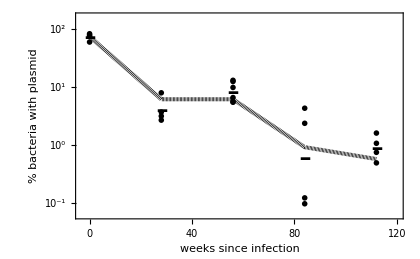

```mathematica
Show[
MyListPlot[
ToLog[{fitdata1,fitdata2}],
Epilog->mylegend3[{"total bacteria","bacteria with plasmid"},{0.05,0.95}],
PlotRange->{{-3,120},{1.999,12.0001}},
FrameLabel->{"days since infection","bacterial count"},
FrameTicks->{myticks,logticks3[{2,12,2}]}
],
MyPlot[Log[10,ssrV2[datasetT,Par0,3]],{t,0,tmax}
],
MyListPlot[AverageData[ToLog[{fitdata1,fitdata2}]],
SymbolShape->Line,
Joined->False
]
]

Show[
MyListPlot[
{Map[{#[[1]],Log[10,#[[2]]]}&,fitdata3]},
PlotRange->{{-3,120},{-1.2001,2.2001}},
FrameLabel->{"weeks since infection","% bacteria with plasmid"},
FrameTicks->{myticks,logticks3[{-3,2,1}]}
],
MyPlot[2+Log[10,ssrV2[datasetT,Par0,4]],{t,0,tmax}
],
MyListPlot[{AverageDataOne[Map[{#[[1]],Log[10,#[[2]]]}&,fitdata3]]},
SymbolShape->Line,
Joined->False
]
]
```

```mathematica
tStart=SessionTime[];

sol=FindMinimum[
ssrV2[datasetT,pars,2],
pars0,
MaxIterations->10^4,
AccuracyGoal->eps,
PrecisionGoal->eps,
Method->Automatic 
];

sol[[2]]=Map[ReplacePart[#,#[[2]]^pow,2]&,sol[[2]]];

Print[sol];
Length[sol[[2]]]
tEnd=SessionTime[];
Print["Simulations ran for ",tEnd-tStart," sec or ",(tEnd-tStart)/60," min"];
Clear[tStart,tEnd];

If[NumericQ[sol[[1]]],Par0=ParD/.sol[[2]]];
pars0=Cases[Table[If[FixedPars[[i]]==0,{ParF[[i]],Par0[[i]]^(1/pow),1.01*Par0[[i]]^(1/pow)}],{i,1,Length[ParF]}],x_?(VectorQ[#]&)];
pars0=Split[Sort[pars0]][[All,1]];
Transpose[{ParF,Par0,FixedPars}]
```

{-1587.49,{d1→0.494365,d2→0.063982,d3→0.691938,d4→8.40859×10^-11,f0→148.466,p0→398.039,r1→0.885201,r2→1.5046×10^-14,r3→0.676476,r4→0.168295,sigma1→0.17185,sigma2→0.0805583}}

12

Simulations ran for 2.99979 sec or 0.0499965 min

{{r1,0.885201,0},{r2,1.5046×10^-14,0},{r3,0.676476,0},{r4,0.168295,0},{d1,0.494365,0},{d2,0.063982,0},{d3,0.691938,0},{d4,8.40859×10^-11,0},{p0,398.039,0},{f0,148.466,0},{sigma1,0.17185,0},{sigma2,0.0805583,0}}

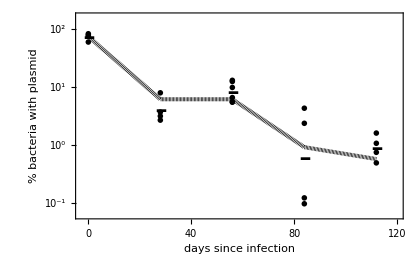
{-Graphics-,-Graphics-}

```mathematica
{Show[
MyListPlot[
ToLog[{fitdata1,fitdata2}],
Epilog->{
mylegend3[{"total bacteria","bacteria with plasmid"},{0.50,0.97}],
mylegend2noS[{
"r="<>ToString[MyRound[{r1,r2,r3,r4}/.sol[[2]],2]],
"δ="<>ToString[MyRound[{d1,d2,d3,d4}/.sol[[2]],2]],
"s="<>ToString[s]
},{-0.01,0.97},FontColor->{Black,Black,Black,Black,Black}]
},
PlotRange->{{-2.5,120},{1.999,12.0001}},
PlotRange->{1.999,12.0001},
FrameLabel->{"days since infection","Mtb/lung"},
FrameTicks->{myticks,logticks3[{2,12,2}]}
],
MyPlot[Log[10,ssrV2[datasetT,Par0,3]],{t,0,tmax}
],
MyListPlot[AverageData[ToLog[{fitdata1,fitdata2}]],
SymbolShape->Line,
Joined->False
]
],

Show[
MyListPlot[
{Map[{#[[1]],Log[10,#[[2]]]}&,fitdata3]},
PlotRange->{{-2.5,120},{-1.2001,2.2001}},
FrameLabel->{"days since infection","% bacteria with plasmid"},
FrameTicks->{myticks,logticks3[{-3,2,1}]}
],
MyPlot[2+Log[10,ssrV2[datasetT,Par0,4]],{t,0,tmax}
],
MyListPlot[{AverageDataOne[Map[{#[[1]],Log[10,#[[2]]]}&,fitdata3]]},
SymbolShape->Line,
Joined->False
]
]}

MyGraphicsArray[%];
```

## 2 granulomas in the lung: corrected data (March 2021, s=0.10)

### Full model (s=0.10): fitting 0-16wk data (in days) - total and % weighted least squares: best fit

```mathematica
data=Import[PicturesPath<>"/data/selvakumar_u17/data-HN878_pBP10-invitro-invivo-TOSHARE.xlsx","XLSX"][[2]];
%//TableForm;

Transpose[{Range[Length[data[[1]]]],data[[1]]}]//TableForm
```

1 | time (weeks)
2 | animal ID
3 | Mtb strain
4 | Mtb type
5 | left or right lung
6 | weight of tissue, g
7 | CFU/tissue
8 | tissue

```mathematica
animals=Split[Sort[Drop[data[[All,2]],1]]][[All,1]]
Length[animals]
lung={"left","right"};
Mtb={"HN878","HN878+pBP10"};
Split[Sort[Drop[data[[All,4]],1]]][[All,1]];
type={"sensitive","sensitive+resistant","resistant"};
```

{506.,507.,509.,510.,511.,512.,513.,514.,515.,516.,517.,518.,519.,520.,521.,522.,523.,524.,525.,526.,527.,528.,529.,}

24

```mathematica
(* HN878+pBP10: percent of plasmid-bearing cells *)

subset=Split[Sort[Cases[data,x_?(#[[3]]==Mtb[[2]]&):>x[[2]]]]][[All,1]];
j=1; (* lung *)
i=2; (* animal *)
tt1=Cases[data,x_?(#[[2]]==subset[[i]]&&#[[5]]==lung[[j]]&&#[[4]]=="sensitive+resistant"&)][[1]]
tt2=Cases[data,x_?(#[[2]]==subset[[i]]&&#[[5]]==lung[[j]]&&#[[4]]=="resistant"&)][[1]]
```

{8.,520.,HN878+pBP10,sensitive+resistant,left,14.7,1.3617×10^7,lung}

{8.,520.,HN878+pBP10,resistant,left,14.7,1.7595×10^6,lung}

```mathematica
Clear[i,j];
(* data formatted in days *)
alldata=Table[
Table[
tt1=Cases[data,x_?(#[[2]]==subset[[i]]&&#[[5]]==lung[[j]]&&#[[4]]=="sensitive+resistant"&)][[1]];
tt2=Cases[data,x_?(#[[2]]==subset[[i]]&&#[[5]]==lung[[j]]&&#[[4]]=="resistant"&)][[1]];
{tt1[[1]]*7,tt1[[7]],tt2[[7]],N[100*tt2[[7]]/tt1[[7]]],lung[[j]]},
{i,1,Length[subset]}],{j,1,Length[lung]}
]
```

{{{28.,2.69151×10^7,844537.,3.13778,left},{56.,1.3617×10^7,1.7595×10^6,12.9213,left},{84.,2.00791×10^6,86053.5,4.28571,left},{56.,1.42194×10^6,175299.,12.3281,left},{0.,314.666,184.663,58.6854,left},{112.,3.2883×10^10,2.46164×10^8,0.748607,left},{28.,2.69242×10^7,989432.,3.67488,left},{56.,739500.,40179.5,5.43333,left},{84.,1.58871×10^6,1556.29,0.0979592,left},{0.,340.8,277.752,81.5,left},{112.,3.48491×10^6,37322.3,1.07097,left}},{{28.,3.51333×10^7,2.76911×10^6,7.88172,right},{56.,2.52923×10^7,2.46267×10^6,9.73684,right},{84.,5.27132×10^6,124471.,2.36129,right},{56.,6.28801×10^6,346874.,5.51643,right},{0.,969.588,714.433,73.6842,right},{112.,1.69568×10^10,2.72023×10^8,1.60421,right},{28.,3.62469×10^7,969553.,2.67486,right},{56.,8.25516×10^6,539371.,6.53374,right},{84.,3.34004×10^6,4128.67,0.123611,right},{0.,847.895,657.966,77.6,right},{112.,2.20479×10^7,108800.,0.493471,right}}}

```mathematica
alldata0=Cases[Flatten[alldata,1],x_?(#[[1]]≤16*7&)];
fitdataL=alldata[[All,1]];
fitdataR=alldata[[All,2]];
```

```mathematica
fitdata1=alldata0[[All,{1,2}]];
fitdata2=alldata0[[All,{1,3}]];
fitdata3=alldata0[[All,{1,4}]];
Print["Total error = ",lof0[ToLogOne[fitdata1]][[1]]+lof0[ToLogOne[fitdata2]][[1]]];
```

Total error = 32.6593

```mathematica
Show[
MyListPlot[
ToLog[{fitdata1,fitdata2}],
Epilog->mylegend3[{"total bacteria","bacteria with plasmid"},{0.05,0.95}],
PlotRange->{{-0.5,20*7},{1.999,12.0001}},
FrameLabel->{"days since infection","bacterial count"},
FrameTicks->{myticks,logticks3[{2,12,2}]}
],
MyListPlot[AverageData[ToLog[{fitdata1,fitdata2}]],
SymbolShape->Line,
Joined->True
]
]

DisplayTogether[
MyListPlot[
{Map[{#[[1]],Log[10,#[[2]]]}&,fitdata3]},
PlotRange->{{-0.5,20*7},{-1.5001,2.2001}},
FrameLabel->{"days since infection","% bacteria with plasmid"},
FrameTicks->{myticks,logticks3[{-3,2,1}]}
],
MyListPlot[{AverageDataOne[Map[{#[[1]],Log[10,#[[2]]]}&,fitdata3]]},
SymbolShape->Line,
Joined->True
]
]
```

-Graphics-

-Graphics-

```mathematica
Clear[ssrV,parV,array];

ssrV3[array_,parV_/;VectorQ[parV,NumericQ],type___]:=Module[
{r1,r2,r3,d1,d2,d3,rr1,rr2,rr3,dd1,dd2,dd3,sol,pp,p,f,ff,pp0,p0,f0,r,d,ff0,PP,FF,FF0,N0,dd,rr,sigma1,sigma2,sigma,result,FF1,r4,d4,rr4,dd4},
{r1,r2,r3,r4,d1,d2,d3,d4,rr1,rr2,rr3,rr4,dd1,dd2,dd3,dd4,p0,f0,pp0,ff0,sigma1,sigma2}=parV;
r[t_]:=If[t<t1,r1,If[t<t2,r2,If[t<t3,r3,r4]]];
d[t_]:=If[t<t1,d1,If[t<t2,d2,If[t<t3,d3,d4]]];
rr[t_]:=If[t<t1,rr1,If[t<t2,rr2,If[t<t3,rr3,rr4]]];
dd[t_]:=If[t<t1,dd1,If[t<t2,dd2,If[t<t3,dd3,dd4]]];
sigma={sigma1,sigma2};

sol=NDSolve[
{
p'[t]==r[t]*(1-s)*p[t]-d[t]*p[t],p[0]==p0,
f'[t]==s*r[t]*p[t]+r[t]*f[t]-d[t]*f[t],f[0]==f0,
pp'[t]==rr[t]*(1-s)*pp[t]-dd[t]*pp[t],pp[0]==pp0,
ff'[t]==s*rr[t]*pp[t]+rr[t]*ff[t]-dd[t]*ff[t],ff[0]==ff0
},
{p[t],f[t],pp[t],ff[t]},
{t,0,tmax},
Method->Automatic
];

PP[t1_]:=First[(p[t]+pp[t])/.sol]/.t->t1;
FF[t1_]:=First[(f[t]+ff[t])/.sol]/.t->t1;
FF1[t_]:={PP[t]+FF[t],PP[t]};
FF0[t_]:={PP[t]+FF[t],100*PP[t]/(PP[t]+FF[t])};
N0[t1_]:={First[(p[t]+f[t])/.sol]/.t->t1,First[(pp[t]+ff[t])/.sol]/.t->t1};

result=
Which[
type==1,Table[Map[(Log[10,FF0[#[[1]]][[i]]]-Log[10,#[[2]]])&,array[[i]]],{i,1,Length[array]}],
type==2,Total[
Flatten[Table[
Map[(Log[10,FF0[#[[1]]][[i]]]-Log[10,#[[2]]])^2/(2*sigma[[i]]^2)&,array[[i]]]+Length[array[[i]]]*Log[sigma[[i]]],
{i,1,Length[array]}
],1]],
type==3,FF1[t],
type==4,{PP[t]/(PP[t]+FF[t])},
type==5,Table[Table[{t,FF1[t][[i]]},{t,0,tmax,tmax/100}],{i,1,2}],
type==6,Table[Table[{t,N0[t][[i]]},{t,0,tmax,tmax/100}],{i,1,2}]
];
Clear[PP,FF,FF0,sol];
result
];

eps=12;


t1=4*7;
t2=8*7;
t3=12*7;
t4=16*7;
allT={t1,t2,t3,t4};

tmax=allT[[-1]];
```

```mathematica
(* Full model *)

datasetT={fitdata1,fitdata3};

Clear[r1,r2,r3,d1,d2,d3,p0,f0];
pow=2;

(* sigma1 and sigma2 *)
s=0.10;
AllPars=
{{r1,1.042866522612197,0},{r2,0.588381533889632,0},{r2,0.588381533889632,0},{r2,0.588381533889632,0},{d1,0.6380542318892081,0},{d1,0.6380542318892081,0},{d1,0.6380542318892081,0},{d1,0.6380542318892081,0},{rr1,0.15705376182118036,0},{rr1,0.15705376182118036,0},{rr3,1.0415250562115141,0},{rr4,0.23409766806900828,0},{dd1,3.1952499547836323*^-9,0},{dd1,3.1952499547836323*^-9,0},{dd3,1.0792604225586777,0},{dd4,3.600023133166618*^-7,0},{p0,204.4639843589038,0},{f0,72.01046087443255,0},{p0,204.4639843589038,0},{f0,72.01046087443255,0},{sigma1,0.1732925174729851,0},{sigma2,0.07334935754202702,0}};

{ParF,Par0,FixedPars}=Transpose[AllPars];

pars=Table[If[FixedPars[[i]]==0,ParF[[i]]^pow,Par0[[i]]],{i,1,Length[ParF]}];
pars0=Cases[Table[If[FixedPars[[i]]==0,{ParF[[i]],Par0[[i]]^(1/pow),1.01*Par0[[i]]^(1/pow)}],{i,1,Length[ParF]}],x_?(VectorQ[#]&)];
pars0=Split[Sort[pars0]][[All,1]];
ParD=(ParF*(1-FixedPars)+Par0*FixedPars);
Print["Parameters to be fitted ",pars0[[All,1]]];

eps=8;

tStart=SessionTime[];
ssrV3[datasetT,Par0,2]
tEnd=SessionTime[];
Print["Calculated in ",tEnd-tStart," sec or ",(tEnd-tStart)/60," min"];
Clear[tStart,tEnd];
```

Parameters to be fitted {d1,dd1,dd3,dd4,f0,p0,r1,r2,rr1,rr3,rr4,sigma1,sigma2}

-1628.51

Calculated in 0.01983 sec or 0.0003305 min

-Graphics-

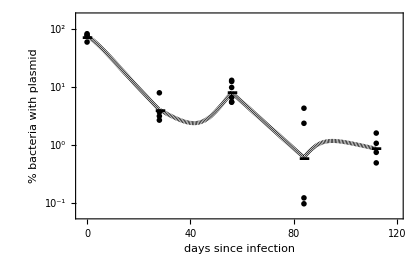

```mathematica
Show[
MyListPlot[
ToLog[{fitdata1,fitdata2}],
Epilog->mylegend3[{"total bacteria","bacteria with plasmid"},{0.05,0.95}],
PlotRange->{{-2,120},{1.999,12.0001}},
FrameLabel->{"days since infection","bacterial count"},
FrameTicks->{myticks,logticks3[{2,12,2}]}
],
MyPlot[Log[10,ssrV3[datasetT,Par0,3]],{t,0,tmax}
],
MyListPlot[AverageData[ToLog[{fitdata1,fitdata2}]],
SymbolShape->Line,
Joined->False
]
]

Show[
MyListPlot[
{Map[{#[[1]],Log[10,#[[2]]]}&,fitdata3]},
PlotRange->{{-2,120},{-1.2001,2.2001}},
FrameLabel->{"days since infection","% bacteria with plasmid"},
FrameTicks->{myticks,logticks3[{-3,2,1}]}
],
MyPlot[2+Log[10,ssrV3[datasetT,Par0,4]],{t,0,tmax}
],
MyListPlot[{AverageDataOne[Map[{#[[1]],Log[10,#[[2]]]}&,fitdata3]]},
SymbolShape->Line,
Joined->False
]
]
```

```mathematica
tStart=SessionTime[];

sol=FindMinimum[
ssrV3[datasetT,pars,2],
pars0,
MaxIterations->10^4,
AccuracyGoal->eps,
PrecisionGoal->eps,
Method->Automatic 
];

sol[[2]]=Map[ReplacePart[#,#[[2]]^pow,2]&,sol[[2]]];

Print[sol];

tEnd=SessionTime[];
Print["Simulations ran for ",tEnd-tStart," sec or ",(tEnd-tStart)/60," min"];
Clear[tStart,tEnd];
Length[sol[[2]]]
If[NumericQ[sol[[1]]],Par0=ParD/.sol[[2]]];
pars0=Cases[Table[If[FixedPars[[i]]==0,{ParF[[i]],Par0[[i]]^(1/pow),1.01*Par0[[i]]^(1/pow)}],{i,1,Length[ParF]}],x_?(VectorQ[#]&)];
pars0=Split[Sort[pars0]][[All,1]];
AllPars=Transpose[{ParF,Par0,FixedPars}]
```

{-1628.62,{d1→0.656779,dd1→2.88817×10^-7,dd3→1.08462,dd4→1.56835×10^-6,f0→68.4293,p0→210.94,r1→1.06097,r2→0.607193,rr1→0.156411,rr3→1.04889,rr4→0.233176,sigma1→0.173641,sigma2→0.0734495}}

Simulations ran for 50.20195 sec or 0.8366991 min

13

{{r1,1.06097,0},{r2,0.607193,0},{r2,0.607193,0},{r2,0.607193,0},{d1,0.656779,0},{d1,0.656779,0},{d1,0.656779,0},{d1,0.656779,0},{rr1,0.156411,0},{rr1,0.156411,0},{rr3,1.04889,0},{rr4,0.233176,0},{dd1,2.88817×10^-7,0},{dd1,2.88817×10^-7,0},{dd3,1.08462,0},{dd4,1.56835×10^-6,0},{p0,210.94,0},{f0,68.4293,0},{p0,210.94,0},{f0,68.4293,0},{sigma1,0.173641,0},{sigma2,0.0734495,0}}

```mathematica
(* One population vs. 2 populations *)logLik[{{-1628.8396106300943,{d1->0.6424876668883974,dd1->3.1952499547836323*^-9,dd3->1.0722265551022359,dd4->0.00006038978184978983,f0->72.61046035989224,p0->204.16110268953818,r1->1.046941455796006,r2->0.5930909424084223,rr1->0.15714601182657442,rr3->1.0338106647280314,rr4->0.23493375160241908,sigma1->0.17331755953360525,sigma2->0.0733339377431663}},
{-1587.7415346802422,{d1->0.4914103906512621,d2->0.06425242690363883,d3->0.6916559210585959,d4->1.376050293094778*^-7,f0->150.5804540667079,p0->394.6370612635137,r1->0.882501395296861,r2->4.059805941372778*^-10,r3->0.6763778579268251,r4->0.16820426630573487,sigma1->0.17191003587037965,sigma2->0.0804856227598889}}
}
]
```

Chi-square value for the test is 82.1962 at 1 df

Probability that the model with fewer parameters fits no worse is 0.

{1,82.1962,0.}

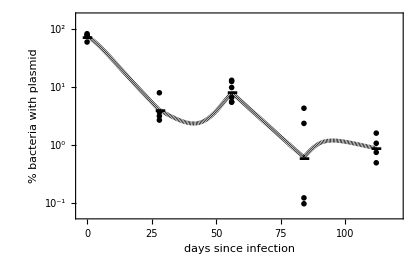
{-Graphics-,-Graphics-,-Graphics-}

```mathematica
printpars=sol[[2]];
printpars=Map[#[[1]]->#[[2]]&,AllPars];

{myFig1=Show[
MyListPlot[
ToLog[{fitdata1,fitdata2}],
Epilog->{
mylegend3[{"total bacteria","bacteria with plasmid"},{0.5,0.97}],
mylegend2noS[{
"r^(1)="<>ToString[MyRound[{r1,r2,r2,r2}/.printpars,2]],
"δ^(1)="<>ToString[MyRound[{d1,d1,d1,d1}/.printpars,2]],
"r^(2)="<>ToString[MyRound[{rr1,rr1,rr3,rr4}/.printpars,2]],
"δ^(2)="<>ToString[MyRound[{dd1,dd1,dd3,dd4}/.printpars,2]],
"s="<>ToString[s]
},{-0.0,0.97},FontColor->{Black,Black,Black,Black,Black}]
},
PlotRange->{{-2,120},{1.999,12.0001}},
FrameLabel->{"days since infection","Mtb/lung"},
FrameTicks->{Automatic,logticks3[{2,12,2}]}
],
MyPlot[Log[10,ssrV3[datasetT,Par0,3]],{t,0,tmax}
],
MyListPlot[AverageData[ToLog[{fitdata1,fitdata2}]],
SymbolShape->Line,
Joined->False
]
],

myFig2=Show[
MyListPlot[
{Map[{#[[1]],Log[10,#[[2]]]}&,fitdata3]},
PlotRange->{{-2,120},{-1.2001,2.2001}},
FrameLabel->{"days since infection","% bacteria with plasmid"},
FrameTicks->{Automatic,logticks3[{-3,2,1}]}
],
MyPlot[2+Log[10,ssrV3[datasetT,Par0,4]],{t,0,tmax}
],
MyListPlot[{AverageDataOne[Map[{#[[1]],Log[10,#[[2]]]}&,fitdata3]]},
SymbolShape->Line,
Joined->False
]
],
myFig3=Show[
MyListPlot[ToLog[ssrV3[datasetT,Par0,6]],
Epilog->{
mylegend[{"population 1","population 2","total"},{0.05,0.97}]
},
PlotRange->{{-2,120},{1.999,12.0001}},
FrameLabel->{"days since infection","Mtb/lung"},
FrameTicks->{Automatic,logticks3[{2,12,2}]},
PlotMarkers->None,
Joined->True
],
MyPlot[{Log[10,ssrV3[datasetT,Par0,3]][[1]]},{t,0,tmax},
PlotStyle->{{Blue,dashings[[3]],Thickness[0.009]}}
]
]
}
MyGraphicsArray[Partition[%,1]];
```

## 3 granulomas in the lung: corrected data (March 2021, s=0.10)

### Full model (s=0.10): fitting 0-16wk data (in days) - total and % weighted least squares: best fit

```mathematica
data=Import[PicturesPath<>"/data/selvakumar_u17/data-HN878_pBP10-invitro-invivo-TOSHARE.xlsx","XLSX"][[2]];
%//TableForm;

Transpose[{Range[Length[data[[1]]]],data[[1]]}]//TableForm
```

1 | time (weeks)
2 | animal ID
3 | Mtb strain
4 | Mtb type
5 | left or right lung
6 | weight of tissue, g
7 | CFU/tissue
8 | tissue

```mathematica
animals=Split[Sort[Drop[data[[All,2]],1]]][[All,1]]
Length[animals]
lung={"left","right"};
Mtb={"HN878","HN878+pBP10"};
Split[Sort[Drop[data[[All,4]],1]]][[All,1]];
type={"sensitive","sensitive+resistant","resistant"};
```

{506.,507.,509.,510.,511.,512.,513.,514.,515.,516.,517.,518.,519.,520.,521.,522.,523.,524.,525.,526.,527.,528.,529.,}

24

```mathematica
(* HN878+pBP10: percent of plasmid-bearing cells *)

subset=Split[Sort[Cases[data,x_?(#[[3]]==Mtb[[2]]&):>x[[2]]]]][[All,1]];
j=1; (* lung *)
i=2; (* animal *)
tt1=Cases[data,x_?(#[[2]]==subset[[i]]&&#[[5]]==lung[[j]]&&#[[4]]=="sensitive+resistant"&)][[1]]
tt2=Cases[data,x_?(#[[2]]==subset[[i]]&&#[[5]]==lung[[j]]&&#[[4]]=="resistant"&)][[1]]
```

{8.,520.,HN878+pBP10,sensitive+resistant,left,14.7,1.3617×10^7,lung}

{8.,520.,HN878+pBP10,resistant,left,14.7,1.7595×10^6,lung}

```mathematica
Clear[i,j];
(* data formatted in days *)
alldata=Table[
Table[
tt1=Cases[data,x_?(#[[2]]==subset[[i]]&&#[[5]]==lung[[j]]&&#[[4]]=="sensitive+resistant"&)][[1]];
tt2=Cases[data,x_?(#[[2]]==subset[[i]]&&#[[5]]==lung[[j]]&&#[[4]]=="resistant"&)][[1]];
{tt1[[1]]*7,tt1[[7]],tt2[[7]],N[100*tt2[[7]]/tt1[[7]]],lung[[j]]},
{i,1,Length[subset]}],{j,1,Length[lung]}
]
```

{{{28.,2.69151×10^7,844537.,3.13778,left},{56.,1.3617×10^7,1.7595×10^6,12.9213,left},{84.,2.00791×10^6,86053.5,4.28571,left},{56.,1.42194×10^6,175299.,12.3281,left},{0.,314.666,184.663,58.6854,left},{112.,3.2883×10^10,2.46164×10^8,0.748607,left},{28.,2.69242×10^7,989432.,3.67488,left},{56.,739500.,40179.5,5.43333,left},{84.,1.58871×10^6,1556.29,0.0979592,left},{0.,340.8,277.752,81.5,left},{112.,3.48491×10^6,37322.3,1.07097,left}},{{28.,3.51333×10^7,2.76911×10^6,7.88172,right},{56.,2.52923×10^7,2.46267×10^6,9.73684,right},{84.,5.27132×10^6,124471.,2.36129,right},{56.,6.28801×10^6,346874.,5.51643,right},{0.,969.588,714.433,73.6842,right},{112.,1.69568×10^10,2.72023×10^8,1.60421,right},{28.,3.62469×10^7,969553.,2.67486,right},{56.,8.25516×10^6,539371.,6.53374,right},{84.,3.34004×10^6,4128.67,0.123611,right},{0.,847.895,657.966,77.6,right},{112.,2.20479×10^7,108800.,0.493471,right}}}

```mathematica
alldata0=Cases[Flatten[alldata,1],x_?(#[[1]]≤16*7&)];
fitdataL=alldata[[All,1]];
fitdataR=alldata[[All,2]];
```

```mathematica
fitdata1=alldata0[[All,{1,2}]];
fitdata2=alldata0[[All,{1,3}]];
fitdata3=alldata0[[All,{1,4}]];
Print["Total error = ",lof0[ToLogOne[fitdata1]][[1]]+lof0[ToLogOne[fitdata2]][[1]]];
```

Total error = 32.6593

```mathematica
Show[
MyListPlot[
ToLog[{fitdata1,fitdata2}],
Epilog->mylegend3[{"total bacteria","bacteria with plasmid"},{0.05,0.95}],
PlotRange->{{-0.5,20*7},{1.999,12.0001}},
FrameLabel->{"days since infection","bacterial count"},
FrameTicks->{myticks,logticks3[{2,12,2}]}
],
MyListPlot[AverageData[ToLog[{fitdata1,fitdata2}]],
SymbolShape->Line,
Joined->True
]
]

DisplayTogether[
MyListPlot[
{Map[{#[[1]],Log[10,#[[2]]]}&,fitdata3]},
PlotRange->{{-0.5,20*7},{-1.5001,2.2001}},
FrameLabel->{"days since infection","% bacteria with plasmid"},
FrameTicks->{myticks,logticks3[{-3,2,1}]}
],
MyListPlot[{AverageDataOne[Map[{#[[1]],Log[10,#[[2]]]}&,fitdata3]]},
SymbolShape->Line,
Joined->True
]
]
```

-Graphics-

-Graphics-

```mathematica
Clear[ssrV4,parV,array];

ssrV4[array_,parV_/;VectorQ[parV,NumericQ],type___]:=Module[
{r1,r2,r3,d1,d2,d3,rr1,rr2,rr3,dd1,dd2,dd3,sol,pp,p,f,ff,pp0,p0,f0,r,d,ff0,PP,FF,FF0,N0,dd,rr,sigma1,sigma2,sigma,result,FF1,r4,d4,rr4,dd4,rrr1,rrr2,rrr3,rrr4,ddd1,ddd2,ddd3,ddd4,ppp0,fff0,rrr,ddd,ppp,fff},
{r1,r2,r3,r4,d1,d2,d3,d4,rr1,rr2,rr3,rr4,dd1,dd2,dd3,dd4,rrr1,rrr2,rrr3,rrr4,ddd1,ddd2,ddd3,ddd4,p0,f0,pp0,ff0,ppp0,fff0,sigma1,sigma2}=parV;
r[t_]:=If[t<t1,r1,If[t<t2,r2,If[t<t3,r3,r4]]];
d[t_]:=If[t<t1,d1,If[t<t2,d2,If[t<t3,d3,d4]]];
rr[t_]:=If[t<t1,rr1,If[t<t2,rr2,If[t<t3,rr3,rr4]]];
dd[t_]:=If[t<t1,dd1,If[t<t2,dd2,If[t<t3,dd3,dd4]]];
rrr[t_]:=If[t<t1,rrr1,If[t<t2,rrr2,If[t<t3,rrr3,rrr4]]];
ddd[t_]:=If[t<t1,ddd1,If[t<t2,ddd2,If[t<t3,ddd3,ddd4]]];

sigma={sigma1,sigma2};

sol=NDSolve[
{
p'[t]==r[t]*(1-s)*p[t]-d[t]*p[t],p[0]==p0,
f'[t]==s*r[t]*p[t]+r[t]*f[t]-d[t]*f[t],f[0]==f0,
pp'[t]==rr[t]*(1-s)*pp[t]-dd[t]*pp[t],pp[0]==pp0,
ff'[t]==s*rr[t]*pp[t]+rr[t]*ff[t]-dd[t]*ff[t],ff[0]==ff0,
ppp'[t]==rrr[t]*(1-s)*ppp[t]-ddd[t]*ppp[t],ppp[0]==ppp0,
fff'[t]==s*rrr[t]*ppp[t]+rrr[t]*fff[t]-ddd[t]*fff[t],fff[0]==fff0
},
{p[t],f[t],pp[t],ff[t],ppp[t],fff[t]},
{t,0,tmax},
Method->Automatic
];

PP[t1_]:=First[(p[t]+pp[t]+ppp[t])/.sol]/.t->t1;
FF[t1_]:=First[(f[t]+ff[t]+fff[t])/.sol]/.t->t1;
FF1[t_]:={PP[t]+FF[t],PP[t]};
FF0[t_]:={PP[t]+FF[t],100*PP[t]/(PP[t]+FF[t])};
N0[t1_]:={First[(p[t]+f[t])/.sol]/.t->t1,First[(pp[t]+ff[t])/.sol]/.t->t1,First[(ppp[t]+fff[t])/.sol]/.t->t1};

result=
Which[
type==1,Table[Map[(Log[10,FF0[#[[1]]][[i]]]-Log[10,#[[2]]])&,array[[i]]],{i,1,Length[array]}],
type==2,Total[
Flatten[Table[
Map[(Log[10,FF0[#[[1]]][[i]]]-Log[10,#[[2]]])^2/(2*sigma[[i]]^2)&,array[[i]]]+Length[array[[i]]]*Log[sigma[[i]]],
{i,1,Length[array]}
],1]],
type==3,FF1[t],
type==4,{PP[t]/(PP[t]+FF[t])},
type==5,Table[Table[{t,FF1[t][[i]]},{t,0,tmax,tmax/100}],{i,1,2}],
type==6,Table[Table[{t,N0[t][[i]]},{t,0,tmax,tmax/100}],{i,1,3}]
];
Clear[PP,FF,FF0,sol];
result
];

eps=12;


t1=4*7;
t2=8*7;
t3=12*7;
t4=16*7;
allT={t1,t2,t3,t4};

tmax=allT[[-1]];
```

```mathematica
(* Full model *)

datasetT={fitdata1,fitdata3};

Clear[r1,r2,r3,d1,d2,d3,p0,f0];
pow=2;


(* ddd1 is fixed at 0 for early dynamics *)
s=0.18;
AllPars=
{{r1,0.5776188842749376,0},{r2,0.056410718132982395,0},{r2,0.056410718132982395,0},{r2,0.056410718132982395,0},{d1,0.14742033527056383,0},{d1,0.14742033527056383,0},{d1,0.14742033527056383,0},{d1,0.14742033527056383,0},{rr1,0.17176209009281604,0},{rr1,0.17176209009281604,0},{rr3,0.7357112715804356,0},{rr1,0.17176209009281604,0},{dd1,0,1},{dd1,0,1},{dd3,0.7383521145172273,0},{dd3,0.7383521145172273,0},{rrr1,0.04965656273701214,0},{rrr1,0.04965656273701214,0},{rrr1,0.04965656273701214,0},{rrr4,0.7228367385839978,0},{ddd1,0,1},{ddd1,0,1},{ddd1,0,1},{ddd4,0.34561102387706544,0},{p0,131.32044140939976,0},{f0,50.35233420364742,0},{p0,131.32044140939976,0},{f0,50.35233420364742,0},{p0,131.32044140939976,0},{f0,50.35233420364742,0},{sigma1,0.17154129960564302,0},{sigma2,0.07330133955311775,0}};

s=0.10;
AllPars=
{{r1,1.0126714037017757,0},{r2,0.5050392464487417,0},{r2,0.5050392464487417,0},{r2,0.5050392464487417,0},{d1,0.5808608054201803,0},{d1,0.5808608054201803,0},{d1,0.5808608054201803,0},{d1,0.5808608054201803,0},{rr1,0.15955721927350666,0},{rr1,0.15955721927350666,0},{rr3,1.3450136109826303,0},{rr1,0.15955721927350666,0},{dd1,0,1},{dd1,0,1},{dd3,1.3261993782075956,0},{dd3,1.3261993782075956,0},{rrr1,0.21876100033994683,0},{rrr1,0.21876100033994683,0},{rrr1,0.21876100033994683,0},{rrr4,0.8959640689494972,0},{ddd1,0.2562778257702693,0},{ddd1,0.2562778257702693,0},{ddd1,0.2562778257702693,0},{ddd1,0.2562778257702693,0},{p0,123.47159051633547,0},{f0,54.225392756306476,0},{p0,123.47159051633547,0},{f0,54.225392756306476,0},{p0,123.47159051633547,0},{f0,54.225392756306476,0},{sigma1,0.17154727230598557,0},{sigma2,0.07333269136938843,0}};


{ParF,Par0,FixedPars}=Transpose[AllPars];

pars=Table[If[FixedPars[[i]]==0,ParF[[i]]^pow,Par0[[i]]],{i,1,Length[ParF]}];
pars0=Cases[Table[If[FixedPars[[i]]==0,{ParF[[i]],Par0[[i]]^(1/pow),1.01*Par0[[i]]^(1/pow)}],{i,1,Length[ParF]}],x_?(VectorQ[#]&)];
pars0=Split[Sort[pars0]][[All,1]];
ParD=(ParF*(1-FixedPars)+Par0*FixedPars);
Print["Parameters to be fitted ",pars0[[All,1]]];

eps=8;

tStart=SessionTime[];
ssrV4[datasetT,Par0,2]
tEnd=SessionTime[];
Print["Calculated in ",tEnd-tStart," sec or ",(tEnd-tStart)/60," min"];
Clear[tStart,tEnd];
```

Parameters to be fitted {d1,dd3,ddd1,f0,p0,r1,r2,rr1,rr3,rrr1,rrr4,sigma1,sigma2}

-1633.52

Calculated in 0.03775 sec or 0.0006291 min

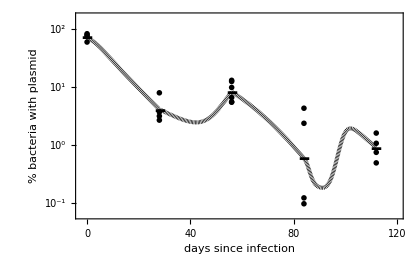
{-Graphics-,-Graphics-}

-Graphics-

```mathematica
{Show[
MyListPlot[
ToLog[{fitdata1,fitdata2}],
Epilog->mylegend3[{"total bacteria","bacteria with plasmid"},{0.05,0.95}],
PlotRange->{{-2,120},{1.999,12.0001}},
FrameLabel->{"days since infection","bacterial count"},
FrameTicks->{myticks,logticks3[{-2,12,2}]}
],
MyPlot[Log[10,ssrV4[datasetT,Par0,3]],{t,0,tmax}
],
MyListPlot[AverageData[ToLog[{fitdata1,fitdata2}]],
SymbolShape->Line,
Joined->False
]
],

Show[
MyListPlot[
{Map[{#[[1]],Log[10,#[[2]]]}&,fitdata3]},
PlotRange->{{-2,120},{-1.2001,2.2001}},
FrameLabel->{"days since infection","% bacteria with plasmid"},
FrameTicks->{myticks,logticks3[{-3,2,1}]}
],
MyPlot[2+Log[10,ssrV4[datasetT,Par0,4]],{t,0,tmax}
],
MyListPlot[{AverageDataOne[Map[{#[[1]],Log[10,#[[2]]]}&,fitdata3]]},
SymbolShape->Line,
Joined->False
]
]}

Show[
MyListPlot[ToLog[ssrV4[datasetT,Par0,6]],
Epilog->{
mylegend[{"population 1","population 2","population 3","total"},{0.05,0.97},FontColor->{Black,Red,colors[[4]],Blue}]
},
PlotRange->{{-2,120},{0,12.0001}},
FrameLabel->{"days since infection","Mtb/lung"},
PlotStyle->{
{colors[[1]],dashings[[1]],Thickness[0.006]},
{colors[[2]],dashings[[2]],Thickness[0.006]},
{colors[[4]],dashings[[4]],Thickness[0.006]}
},

FrameTicks->{Automatic,logticks3[{-2,12,2}]},
PlotMarkers->None,
Joined->True
],
MyPlot[{Log[10,ssrV4[datasetT,Par0,3]][[1]]},{t,0,tmax},
PlotStyle->{{colors[[3]],dashings[[3]],Thickness[0.008]}}
]
]
```

```mathematica
tStart=SessionTime[];

sol=FindMinimum[
ssrV4[datasetT,pars,2],
pars0,
MaxIterations->10^4,
AccuracyGoal->eps,
PrecisionGoal->eps,
Method->Automatic 
];

sol[[2]]=Map[ReplacePart[#,#[[2]]^pow,2]&,sol[[2]]];

Print[sol];
Length[sol[[2]]]
tEnd=SessionTime[];
Print["Simulations ran for ",tEnd-tStart," sec or ",(tEnd-tStart)/60," min"];
Clear[tStart,tEnd];

If[NumericQ[sol[[1]]],Par0=ParD/.sol[[2]]];
pars0=Cases[Table[If[FixedPars[[i]]==0,{ParF[[i]],Par0[[i]]^(1/pow),1.01*Par0[[i]]^(1/pow)}],{i,1,Length[ParF]}],x_?(VectorQ[#]&)];
pars0=Split[Sort[pars0]][[All,1]];
AllPars=Transpose[{ParF,Par0,FixedPars}]
```

{-1633.67,{d1→0.599714,dd3→1.31773,ddd1→0.257412,f0→52.0229,p0→124.215,r1→1.031,r2→0.525262,rr1→0.159864,rr3→1.33573,rrr1→0.23226,rrr4→0.86032,sigma1→0.171495,sigma2→0.0733702}}

13

Simulations ran for 88.736797 sec or 1.4789466 min

{{r1,1.031,0},{r2,0.525262,0},{r2,0.525262,0},{r2,0.525262,0},{d1,0.599714,0},{d1,0.599714,0},{d1,0.599714,0},{d1,0.599714,0},{rr1,0.159864,0},{rr1,0.159864,0},{rr3,1.33573,0},{rr1,0.159864,0},{dd1,0,1},{dd1,0,1},{dd3,1.31773,0},{dd3,1.31773,0},{rrr1,0.23226,0},{rrr1,0.23226,0},{rrr1,0.23226,0},{rrr4,0.86032,0},{ddd1,0.257412,0},{ddd1,0.257412,0},{ddd1,0.257412,0},{ddd1,0.257412,0},{p0,124.215,0},{f0,52.0229,0},{p0,124.215,0},{f0,52.0229,0},{p0,124.215,0},{f0,52.0229,0},{sigma1,0.171495,0},{sigma2,0.0733702,0}}

-Graphics-

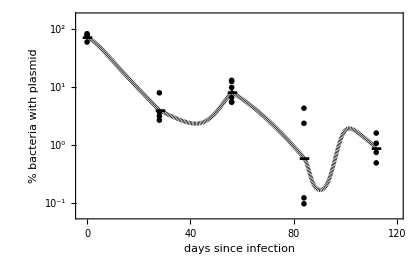

```mathematica
printpars=sol[[2]];
printpars=Map[#[[1]]->#[[2]]&,AllPars];
xticks=LinTicks[0,120,MajorTickLength->{0.02,0},MinorTickLength->{0.,0}];
myFig1=Show[
MyListPlot[
ToLog[{fitdata1,fitdata2}],
Epilog->{
mylegend3[{"total bacteria","bacteria with plasmid"},{0.5,0.97}],
mylegend2noS[{
"r^(1)="<>ToString[MyRound[Take[ParF,4]/.printpars,2]],
"δ^(1)="<>ToString[MyRound[Take[ParF,{5,8}]/.printpars,2]],
"r^(2)="<>ToString[MyRound[Take[ParF,{9,12}]/.printpars,2]],
"δ^(2)="<>ToString[MyRound[Take[ParF,{13,16}]/.printpars,2]],
"r^(3)="<>ToString[MyRound[Take[ParF,{17,20}]/.printpars,2]],
"δ^(3)="<>ToString[MyRound[Take[ParF,{21,24}]/.printpars,2]],
"s="<>ToString[s]
},{-0.0,0.97},FontColor->{Black,Black,Black,Black,Black,Black,Black}]
},
PlotRange->{{-2,120},{1.999,12.0001}},
FrameLabel->{"days since infection","Mtb/lung"},
FrameTicks->{xticks,logticks3[{2,12,2}]}
],
MyPlot[Log[10,ssrV4[datasetT,Par0,3]],{t,0,tmax}
],
MyListPlot[AverageData[ToLog[{fitdata1,fitdata2}]],
SymbolShape->Line,
Joined->False
]
]

myFig2=Show[
MyListPlot[
{Map[{#[[1]],Log[10,#[[2]]]}&,fitdata3]},
PlotRange->{{-2,120},{-1.2001,2.2001}},
FrameLabel->{"days since infection","% bacteria with plasmid"},
FrameTicks->{xticks,logticks3[{-3,2,1}]}
],
MyPlot[2+Log[10,ssrV4[datasetT,Par0,4]],{t,0,tmax}
],
MyListPlot[{AverageDataOne[Map[{#[[1]],Log[10,#[[2]]]}&,fitdata3]]},
SymbolShape->Line,
Joined->False
]
]
```

```mathematica
myFig3=Show[
MyListPlot[ToLog[ssrV4[datasetT,Par0,6]],
Epilog->{
mylegend[{"population 1","population 2","population 3","total"},{0.05,0.97},FontColor->{Black,Red,colors[[4]],Blue}]
},
PlotRange->{{-2,120},{0,12.0001}},
FrameLabel->{"days since infection","Mtb/lung"},
PlotStyle->{
{colors[[1]],dashings[[1]],Thickness[0.006]},
{colors[[2]],dashings[[2]],Thickness[0.006]},
{colors[[4]],dashings[[4]],Thickness[0.006]}
},

FrameTicks->{xticks,logticks3[{-2,12,2}]},
PlotMarkers->None,
Joined->True
],
MyPlot[{Log[10,ssrV4[datasetT,Par0,3]][[1]]},{t,0,tmax},
PlotStyle->{{colors[[3]],dashings[[3]],Thickness[0.008]}}
]
]
```

-Graphics-

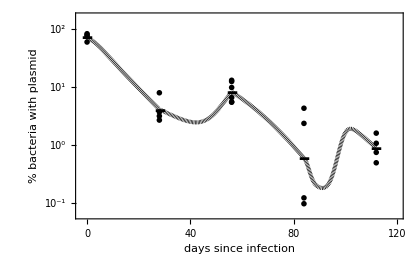
{-Graphics-,-Graphics-,-Graphics-}

```mathematica
{myFig1,myFig2,myFig3}
MyGraphicsArray[Partition[%,1]];
```

```mathematica
(* Comparing 3 vs. 2 population model fit *)

sol1={-1628.8396106300943,{d1->0.6424876668883974,dd1->3.1952499547836323*^-9,dd3->1.0722265551022359,dd4->0.00006038978184978983,f0->72.61046035989224,p0->204.16110268953818,r1->1.046941455796006,r2->0.5930909424084223,rr1->0.15714601182657442,rr3->1.0338106647280314,rr4->0.23493375160241908,sigma1->0.17331755953360525,sigma2->0.0733339377431663}};

sol2={-1633.8318482998006,{d1->0.58184233754708,dd3->1.3224754725211316,ddd1->0.25755861430249133,f0->54.26031872442672,p0->124.28872436541425,r1->1.013273431080182,r2->0.50650665426534,rr1->0.15955763274380255,rr3->1.3409508037353104,rrr1->0.22033687087840567,rrr4->0.8959659048853112,sigma1->0.17154563035694584,sigma2->0.07333105867836538}};

aicLik[{sol1,sol2,Length[Flatten[datasetT,1]]}]
```

Min AICc = -3229.53

AICc = -3219.55 weight = 0.00674465 for model {-1628.84,{d1→0.642488,dd1→3.19525×10^-9,dd3→1.07223,dd4→0.0000603898,f0→72.6105,p0→204.161,r1→1.04694,r2→0.593091,rr1→0.157146,rr3→1.03381,rr4→0.234934,sigma1→0.173318,sigma2→0.0733339}}

AICc = -3229.53 weight = 0.993255 for model {-1633.83,{d1→0.581842,dd3→1.32248,ddd1→0.257559,f0→54.2603,p0→124.289,r1→1.01327,r2→0.506507,rr1→0.159558,rr3→1.34095,rrr1→0.220337,rrr4→0.895966,sigma1→0.171546,sigma2→0.0733311}}

{0.00674465,0.993255}

```mathematica
(* Comparing 3 vs. 1 population model fit *)

sol1={-1567.0521057052497,{d1->0.09881157038475255,d2->0.06403240738788044,d3->0.3542300352090569,d4->6.995287240742571*^-13,f0->150.98164167718733,p0->394.02329337990955,r1->0.48980412945536195,r2->9.302217058439578*^-16,r3->0.3479183061382406,r4->0.1500242117453472,sigma1->0.17342016601559665,sigma2->0.08326949915320976}};

sol2={-1634.0361987393096,{d1->0.14761803600495704,dd3->0.6698391189221092,ddd1->0.08644866702033806,f0->50.27933345383517,p0->131.4570824926779,r1->0.5777956037235089,r2->0.056505032929473856,rr1->0.17181271566713202,rr3->0.6671619868906101,rrr1->0.13032416962464988,rrr4->0.4810010548800898,sigma1->0.17153999757339047,sigma2->0.07330144843723425}};

logLik[{sol1,sol2}]
```

Chi-square value for the test is 133.968 at 1 df

Probability that the model with fewer parameters fits no worse is 0.

{1,133.968,0.}

```mathematica
Show[
MyListPlot[ToLog[ssrV4[datasetT,Par0,6]],
Epilog->{
mylegend[{"population 1","population 2","population 3","total"},{0.05,0.97}]
},
PlotRange->{{-2,120},{1.999,12.0001}},
FrameLabel->{"days since infection","Mtb/lung"},
FrameTicks->{xticks,logticks3[{2,12,2}]},
PlotMarkers->None,
Joined->True
],
MyPlot[{Log[10,ssrV4[datasetT,Par0,3]][[1]]},{t,0,tmax},
PlotStyle->{{colors[[4]],dashings[[4]],Thickness[0.006]}}
]
]
```

-Graphics-